# Tension of the E_G statistic and RSD data with Planck/ΛCDM and implications for weakening gravity. Numerical Analysis and Construction Figures File

## Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
(* In order to use the Needs["ErrorBarLogPlots`"] command you need to install the "Error Bar Log Plots" package which can be installed directly from the zip file "ErrorBarLogPlots.zip" or you can download it from http://library.wolfram.com/infocenter/MathSource/6747/*)

Needs["ErrorBarLogPlots`"]
Off[General::"obspkg",NIntegrate::"inumr",NIntegrate::ncvb,CompiledFunction::cflist,ListInterpolation::inhr,FindMinimum::lstol,Part::partw,NonlinearModelFit::cvmit];
```

## Parameter values

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"] 

(* Planck parameter Values for Planck18 *)

ompl=0.3153;
nn=2;
mm=2 ;
omplerr=0.0073;
h0pl=0.6727;
h0plerr=0.0066;
σ8pl=0.8111;
σ8plerr=0.006;
```

## Datasets

```mathematica
(* Data fσ8  *)

datafσ8={{0.35,0.44,0.05},{0.77,0.49,0.18},{0.17,0.51,0.06},{0.02,0.314,0.048},{0.02,0.398,0.065},{0.25,0.3512,0.0583},{0.37,0.4602,0.0378},{0.25,0.3665,0.0601},{0.37,0.4031,0.0586},{0.44,0.413,0.08},{0.6,0.39,0.063},{0.73,0.437,0.072},{0.067,0.423,0.055},{0.3,0.407,0.055},{0.4,0.419,0.041},{0.5,0.427,0.043},{0.6,0.433,0.067},{0.8,0.47,0.08},{0.35,0.429,0.089},{0.18,0.36,0.09},{0.38,0.44,0.06},{0.32,0.384,0.095},{0.32,0.48,0.1},{0.57,0.417,0.045},{0.15,0.49,0.145},{0.1,0.37,0.13},{1.4,0.482,0.116},{0.59,0.488,0.06},{0.38,0.497,0.045},{0.51,0.458,0.038},{0.61,0.436,0.034},{0.38,0.477,0.051},{0.51,0.453,0.05},{0.61,0.41,0.044},{0.76,0.44,0.04},{1.05,0.28,0.08},{0.32,0.427,0.056},{0.57,0.426,0.029},{0.727,0.296,0.0765},{0.02,0.428,0.0465},{0.6,0.55,0.12},{0.86,0.4,0.11},{0.1,0.48,0.16},{0.001,0.505,0.085},{0.85,0.45,0.11},{0.31,0.384,0.083},{0.36,0.409,0.098},{0.4,0.461,0.086},{0.44,0.426,0.062},{0.48,0.458,0.063},{0.52,0.483,0.075},{0.56,0.472,0.063},{0.59,0.452,0.061},{0.64,0.379,0.054}, {0.1,0.376,0.038},{1.52,0.42,0.076},{1.52,0.396,0.079},{0.978,0.379,0.176},{1.23,0.385,0.099},{1.526,0.342,0.07},{1.944,0.364,0.106},{0.60,0.49,0.12},{0.86,0.46,0.09},{0.57,0.501,0.051},{0.03,0.404,0.0815},{0.72,0.454,0.139}} ;
```

```mathematica
(* Data fσ8 with fiducial cosmology *)

datafσ8fid={{0.35,0.44,0.05,0.25},{0.77,0.49,0.18,0.25},{0.17,0.51,0.06,0.3},{0.02,0.314,0.048,0.266},{0.02,0.398,0.065,0.3},{0.25,0.3512,0.0583,0.25},{0.37,0.4602,0.0378,0.25},{0.25,0.3665,0.0601,0.25},{0.37,0.4031,0.0586,0.25},{0.44,0.413,0.08,0.27},{0.6,0.39,0.063,0.27},{0.73,0.437,0.072,0.27},{0.067,0.423,0.055,0.27},{0.3,0.407,0.055,0.25},{0.4,0.419,0.041,0.25},{0.5,0.427,0.043,0.25},{0.6,0.433,0.067,0.25},{0.8,0.47,0.08,0.25},{0.35,0.429,0.089,0.25},{0.18,0.36,0.09,0.27},{0.38,0.44,0.06,0.27},{0.32,0.384,0.095,0.274},{0.32,0.48,0.1,0.274},{0.57,0.417,0.045,0.274},{0.15,0.49,0.145,0.31},{0.1,0.37,0.13,0.3},{1.4,0.482,0.116,0.27},{0.59,0.488,0.06,0.307115},{0.38,0.497,0.045,0.31},{0.51,0.458,0.038,0.31},{0.61,0.436,0.034,0.31},{0.38,0.477,0.051,0.31},{0.51,0.453,0.05,0.31},{0.61,0.41,0.044,0.31},{0.76,0.44,0.04,0.308},{1.05,0.28,0.08,0.308},{0.32,0.427,0.056,0.31},{0.57,0.426,0.029,0.31},{0.727,0.296,0.0765,0.31},{0.02,0.428,0.0465,0.3},{0.6,0.55,0.12,0.3},{0.86,0.4,0.11,0.3},{0.1,0.48,0.16,0.25},{0.001,0.505,0.085,0.31},{0.85,0.45,0.11,0.3},{0.31,0.384,0.083,0.307},{0.36,0.409,0.098,0.307},{0.4,0.461,0.086,0.307},{0.44,0.426,0.062,0.307},{0.48,0.458,0.063,0.307},{0.52,0.483,0.075,0.307},{0.56,0.472,0.063,0.307},{0.59,0.452,0.061,0.307},{0.64,0.379,0.054,0.307},     {0.1,0.376,0.038,0.282},{1.52,0.42,0.076,0.26479},{1.52,0.396,0.079,0.31},{0.978,0.379,0.176,0.31},{1.23,0.385,0.099,0.31},{1.526,0.342,0.07,0.31},{1.944,0.364,0.106,0.31},{0.60,0.49,0.12,0.31},{0.86,0.46,0.09,0.31},{0.57,0.501,0.051,0.307},{0.03,0.404,0.0815,0.3121},{0.72,0.454,0.139,0.31}} ;
```

```mathematica
(* Data  Eg(z)*)

dataeg={{0.267,0.43,0.13},{0.27,0.4,0.05},{0.27,0.46,0.085},{0.305,0.27,0.08},{0.32,0.4,0.09},{0.32,0.48,0.1},{0.32,0.39,0.06},{0.554,0.26,0.07},{0.57,0.31,0.06},{0.57,0.3,0.07},{0.57,0.24,0.06},{0.57,0.42,0.056},{0.57,0.39,0.05},{0.57,0.43,0.1},{0.6,0.16,0.09},{0.86,0.09,0.07}};

dataegb={{0.267,0.43,0.13},{0.272,0.4,0.05},{0.275,0.46,0.085},{0.305,0.27,0.08},{0.32,0.4,0.09},{0.325,0.48,0.1},{0.33,0.39,0.06},{0.554,0.26,0.07},{0.57,0.31,0.06},{0.575,0.3,0.07},{0.58,0.24,0.06},{0.585,0.42,0.056},{0.56,0.39,0.05},{0.565,0.43,0.1},{0.6,0.16,0.09},{0.86,0.09,0.07}};
```

## Theoretical Expressions

```mathematica
(* The fσ8  and the Subscript[E, G] observables *)

H[a_,w_,om_]:=√(om a^-3+(1-om)a^(-3(1+w)))
dLh[a_,om_,w_]:=2/(a √om)(Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),1-1/om]-√a Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),(1-1/om)a^(-3w)])
amin=0.001;

Geff[a_,ga_,n_]:=1+ga(1-a)^n-ga(1-a)^(2n);
Gl[z_,gb_,m_]:=1+gb(z/(1+z))^m-gb(z/(1+z))^(2m);

dsol[om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ]:=(dsol[om,w,ga,n]=Module[{a},NDSolve[{-((3 om d[a] Geff[a,ga,n])/(2 a^5  H[a,w,om]^2))+d'[a] (3/a+D[H[a,w,om],a]/H[a,w,om])+d''[a]==0,d[amin]==amin,d'[amin]==1},d,{a,amin,1}][[1]]])

Da[a_,om_,w_,ga_,n_]:=d[a]/.dsol[om,w,ga,n]
fa[aa_,om_,w_,ga_,n_]:=a d'[a]/d[a]/.a->aa/.dsol[om,w,ga,n]

fσ8geff[a_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ,σ8_?NumberQ]:=(σ8 Da[aa,om,w,ga,n])/Da[1,om,w,ga,n] fa[aa,om,w,ga,n]/.aa->a
fσ8z[z_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ,σ8_?NumberQ]:=(σ8 Da[aa,om,w,ga,n])/Da[1,om,w,ga,n] fa[aa,om,w,ga,n]/.aa->1/(1+z)

ffz[z_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ]:=fa[aa,om,w,ga,n]/.aa->1/(1+z)

ratio1[z_,w_,om_,omfid_]:=((H[a,w,om] dLh[a,om,w])/(H[a,-1,omfid] dLh[a,omfid,-1]))^(-1)/.a->1/(1+z);



eg[z_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,gb_?NumberQ,n_?NumberQ,m_?NumberQ]:=(om   Gl[z,gb,m]) /ffz[z,om,w,ga,n]
```

```mathematica
(* Sigma Difference of terms*)

dchi[nsig_,M_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]//N
nsig[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2}][[1,2]]
```

## Figure 7

```mathematica
(* Covariance Matrix for data  fσ8*)


Cijwigglez=10^-3*({{6.400, 2.570, 0.000}, {2.570, 3.969, 2.540}, {0.000, 2.540, 5.184}});

Wigglez={10,11,12};
Cijfσ8=DiagonalMatrix[datafσ8fid[[All,3]]^2];
Cijfσ8[[Wigglez,Wigglez]]=Cijwigglez;
InvCijfσ8=Inverse[Cijfσ8];
```

```mathematica
(* Correlated χ^2 term for fσ8 with fiducial cosmology *)

vecfσ8[data_,w_,om_,ga_,n_,σ8_]:=Table[data[[i,2]]-ratio1[data[[i,1]],w,om,data[[i,4]]]fσ8geff[1/(1+data[[i,1]]),om,w,ga,n,σ8],{i,1,Length[data]}]
chi2fid[data_,w_,om_,ga_,n_,σ8_]:=vecfσ8[data,w,om,ga,n,σ8].InvCijfσ8.vecfσ8[data,w,om,ga,n,σ8]
```

```mathematica
(* Minimization of χ^2 for data fσ8 with fiducial cosmology *)

chi2minfσ8=FindMinimum[chi2fid[datafσ8fid,-1,om,ga,2,σ8],{om,0.30,0.31},{ga,0,-1},{σ8,0.8,0.81}]
```

{32.0423,{om→0.272466,ga→-1.30663,σ8→0.885758}}

```mathematica
(* Tension level in the  3D parameter space (Subscript[Ω, 0m], Subscript[g, a], σ8) with fiducial cosmology *)

dchifσ8omgaσ8=chi2fid[datafσ8fid,-1,ompl,0,2,σ8pl]-chi2minfσ8[[1]];
nsigfσ8omgaσ8[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,4}][[1,2]]
nsigfσ8omgaσ8[dchifσ8omgaσ8,3]
```

3.69556

```mathematica
(* 1σ  standard deviations with fiducial cosmology*)

fσ8s1om=FindRoot[chi2fid[datafσ8fid,-1,om,chi2minfσ8[[2,2,2]],2,chi2minfσ8[[2,3,2]]]==chi2minfσ8[[1]]+1,{om,chi2minfσ8[[2,1,2]]+0.5}][[1,2]]-chi2minfσ8[[2,1,2]];
fσ8s1ga=FindRoot[chi2fid[datafσ8fid,-1,chi2minfσ8[[2,1,2]],ga,2,chi2minfσ8[[2,3,2]]]==chi2minfσ8[[1]]+1,{ga,chi2minfσ8[[2,2,2]]+0.5}][[1,2]]-chi2minfσ8[[2,2,2]];
fσ8s1σ8=FindRoot[chi2fid[datafσ8fid,-1,chi2minfσ8[[2,1,2]],chi2minfσ8[[2,2,2]],2,σ8]==chi2minfσ8[[1]]+1,{σ8,chi2minfσ8[[2,3,2]]+0.5}][[1,2]]-chi2minfσ8[[2,3,2]];

Print["1σ Ωm=",fσ8s1om]
Print["1σ ga=",fσ8s1ga]
Print["1σ σ8=",fσ8s1σ8]
```

1σ Ωm=0.018718

1σ ga=0.139569

1σ σ8=0.0154297

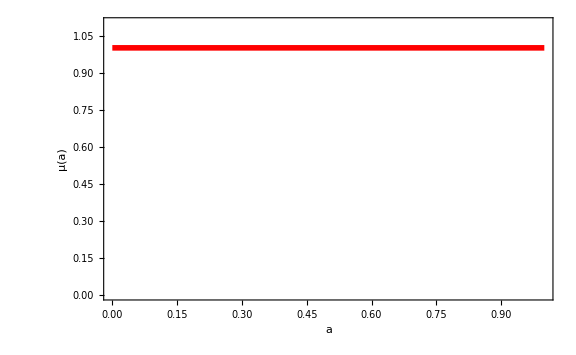

```mathematica
(* Plot μ(z) and  best fit on dataset with 1σ deviation *)

plotμgr=Plot[Geff[a,0,0],{a,0,1},Frame->True,FrameLabel->{"a","μ(a)"},BaseStyle->FontSize->18,PlotStyle->{PointSize->Large,Thickness[0.007],Red},PlotRange->{{0,1},{0,1.1}},Axes->False,ImageSize->Large]
```

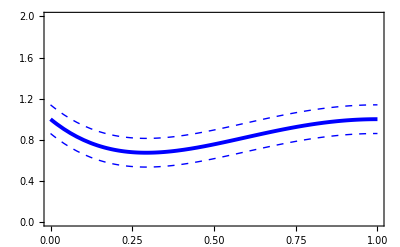

```mathematica
plfσ8μbfs=Plot[{Geff[a,chi2minfσ8[[2,2,2]],2]+fσ8s1ga,Geff[a,chi2minfσ8[[2,2,2]],2],Geff[a,chi2minfσ8[[2,2,2]],2]-fσ8s1ga},{a,0,1},PlotRange->{{0,1},{0,2}},Frame->True,PlotStyle->{{PointSize->Large,Dashed,Thick,Blue},{PointSize->Large,Thickness[0.007],Blue},{PointSize->Large,Dashed,Thick,Blue}},Axes->False]
```

```mathematica
(* Covariance Matrix for data  Eg*)

Cijeg=DiagonalMatrix[dataeg[[All,3]]^2];
InvCijeg=Inverse[Cijeg];
Cijeg//MatrixForm;
```

```mathematica
(* Correlated χ^2 term for Eg*)

veceg[data_,w_,om_,ga_,gb_,n_,m_]:=Table[(data[[i,2]]-eg[data[[i,1]],om,w,ga,gb,n,m]),{i,1,Length[data]}];
chi2eg[data_,w_,om_,ga_,gb_,n_,m_]:=veceg[data,w,om,ga,gb,n,m].InvCijeg.veceg[data,w,om,ga,gb,n,m]
```

```mathematica
(* Minimization of χ^2 for data Eg*)
```

```mathematica
chi2mineg=FindMinimum[chi2eg[dataeg,-1,om,ga,gb,2,2],{om,0.31},{ga,0},{gb,0}]
```

{21.1404,{om→0.312923,ga→-0.1295,gb→-2.30782}}

```mathematica
(* 1σ  standard deviations  *)

egs1om=FindRoot[chi2eg[dataeg,-1,om,chi2mineg[[2,2,2]],chi2mineg[[2,3,2]],2,2]==chi2mineg[[1]]+1,{om,chi2mineg[[2,1,2]]+0.5}][[1,2]]-chi2mineg[[2,1,2]];
egs1ga=FindRoot[chi2eg[dataeg,-1,chi2mineg[[2,1,2]],ga,chi2mineg[[2,3,2]],2,2]==chi2mineg[[1]]+1,{ga,chi2mineg[[2,2,2]]+0.5}][[1,2]]-chi2mineg[[2,2,2]];
egs1gb=FindRoot[chi2eg[dataeg,-1,chi2mineg[[2,1,2]],chi2mineg[[2,2,2]],gb,2,2]==chi2mineg[[1]]+1,{gb,chi2mineg[[2,3,2]]+0.5}][[1,2]]-chi2mineg[[2,3,2]];

Print["1σ Ωm=",egs1om]
Print["1σ ga=",egs1ga]
Print["1σ gb=",egs1gb]
```

1σ Ωm=0.0243368

1σ ga=0.490402

1σ gb=0.422686

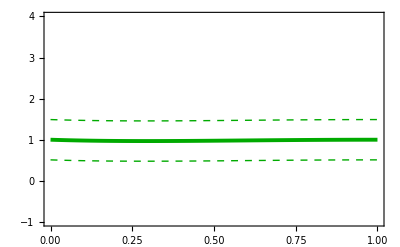

```mathematica
plegμbfs=Plot[{Geff[a,chi2mineg[[2,2,2]],2]+egs1ga,Geff[a,chi2mineg[[2,2,2]],2],Geff[a,chi2mineg[[2,2,2]],2]-egs1ga},{a,0,1},PlotRange->{{0,1},{-1,4}},Frame->True,PlotStyle->{{PointSize->Large,Dashed,Thick,Darker[Green]},{PointSize->Large,Thickness[0.007],Darker[Green]},{PointSize->Large,Dashed,Thick,Darker[Green]}},Axes->False]
```

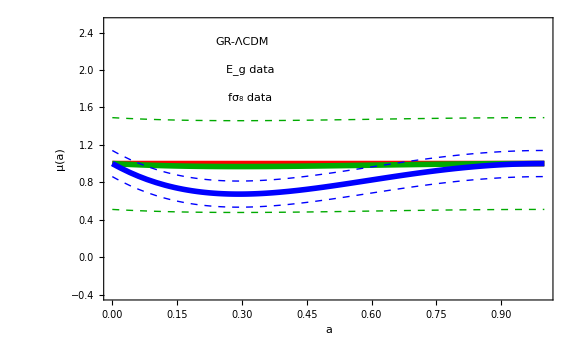

```mathematica
figμzbfs=Show[plotμgr,plegμbfs,plfσ8μbfs,Graphics[{Inset[" GR-ΛCDM ",{0.3,2.3},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",16}]}],Graphics[{Inset["  fσ_8 data ",{0.32,1.7},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",16}]}],Graphics[{Inset["  E_g data ",{0.32,2.0},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",16}]}],PlotRange->{{0,1},{-0.4,2.5}},FrameLabel->{"a","μ(a)"},BaseStyle->{FontFamily->"Times",16},FrameStyle->Directive[Black,Thick],ImageSize->Large]
Export[NotebookDirectory[]<>"figμzbfsall.pdf",figμzbfs,ImageResolution->1000];
```

```mathematica
Gla[a_,gb_,m_]:=1+gb(1-a)^m-gb(1-a)^(2m);
```

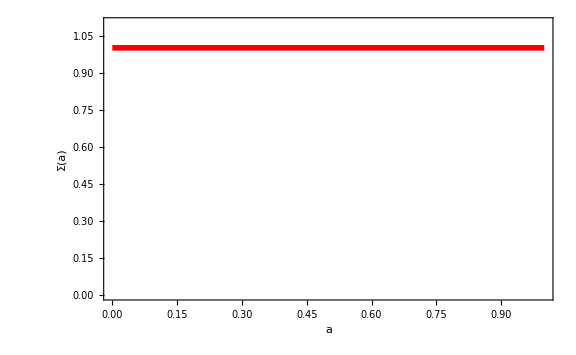

```mathematica
plotΣgr=Plot[Gla[a,0,0],{a,0,1},Frame->True,FrameLabel->{"a","Σ(a)"},BaseStyle->FontSize->18,PlotStyle->{PointSize->Large,Thickness[0.007],Red},PlotRange->{{0,1},{0,1.1}},Axes->False,ImageSize->Large]
```

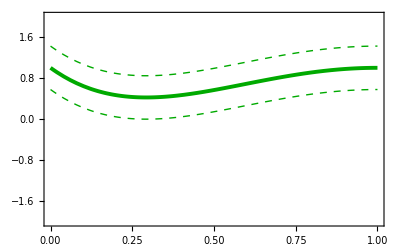

```mathematica
plegΣbfs=Plot[{Gla[a,chi2mineg[[2,3,2]],2]+egs1gb,Gla[a,chi2mineg[[2,3,2]],2],Gla[a,chi2mineg[[2,3,2]],2]-egs1gb},{a,0,1},PlotRange->{{0,1},{-2,2}},Frame->True,PlotStyle->{{PointSize->Large,Dashed,Thick,Darker[Green]},{PointSize->Large,Thickness[0.007],Darker[Green]},{PointSize->Large,Dashed,Thick,Darker[Green]}},Axes->False]
```

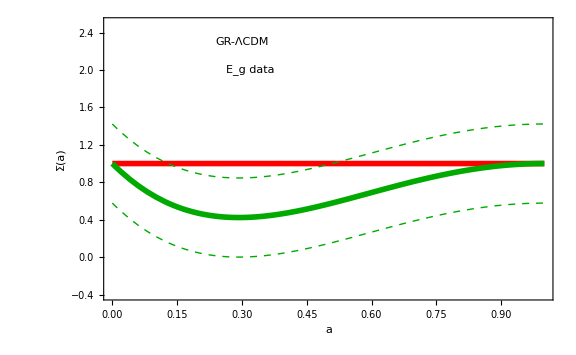

```mathematica
figΣzbfs=Show[plotΣgr,plegΣbfs,Graphics[{Inset[" GR-ΛCDM ",{0.3,2.3},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",16}]}],Graphics[{Inset["  E_g data ",{0.32,2},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",16}]}],PlotRange->{{0,1},{-0.4,2.5}},FrameLabel->{"a","Σ(a)"},BaseStyle->{FontFamily->"Times",16},FrameStyle->Directive[Black,Thick],ImageSize->Large]
Export[NotebookDirectory[]<>"figΣzbfsall.pdf",figΣzbfs,ImageResolution->1000];
```

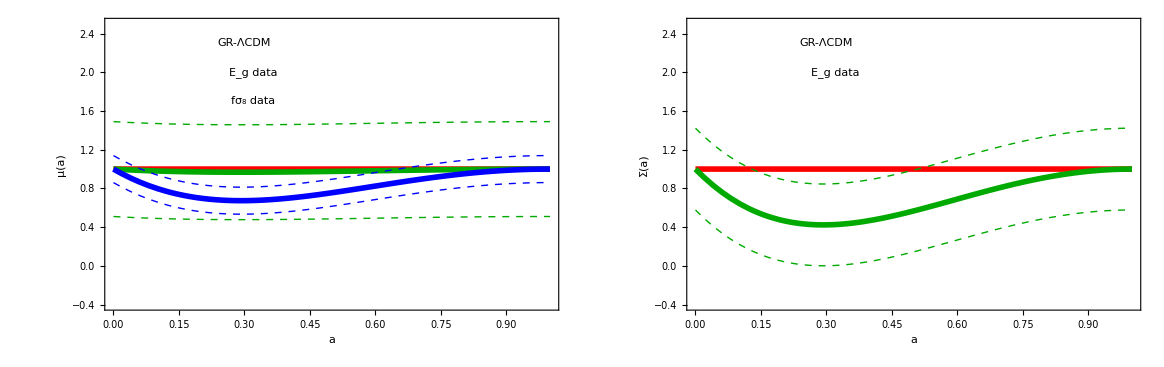

```mathematica
fig9=GraphicsGrid[{{figμzbfs,figΣzbfs}},Spacings->0]
Export[NotebookDirectory[]<>"fig9.pdf",fig9,ImageResolution->1000];
```